```mathematica
p1={1,2,3}
```

{1,2,3}

```mathematica
Graphics3D[{Red,PointSize[.02],Point[p1]},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5]
```

-Graphics3D-

```mathematica
p2={5,3,2};
```

```mathematica
(*comments look like this *)
```

```mathematica
Show[
Graphics3D[{Red,PointSize[.02],Point[p1]},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5],
Graphics3D[{Blue,PointSize[.02],Point[p2]}]
]
```

-Graphics3D-

```mathematica
v12=p2-p1
```

{4,1,-1}

```mathematica
Show[
Graphics3D[{Red,PointSize[.02],Point[p1]},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5],
Graphics3D[{Blue,PointSize[.02],Point[p2]}],
Graphics3D[Arrow[{p1,p1+v12}]]
]
```

-Graphics3D-

```mathematica
(* conceptually speaking, the p1+v12 says start at p1 and go in the p1+v12 direction*)
Norm[v12]
```

3 √2

```mathematica
ahat=Normalize[v12]
```

{(2 √2)/3,1/(3 √2),-1/(3 √2)}

```mathematica
(*this is the command for unit vectors (Normalize) *)
```

```mathematica
a={a1,a2,a3}
```

{a1,a2,a3}

```mathematica
b={b1,b2,b3}
```

{b1,b2,b3}

```mathematica
a.b
```

a1 b1+a2 b2+a3 b3

```mathematica
Normalize[a]
```

{a1/(√(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2)),a2/(√(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2)),a3/(√(Abs[a1]^2+Abs[a2]^2+Abs[a3]^2))}

```mathematica
(*day 2: LINES AND PLANES STARTS HERE --------------------------*)
```

```mathematica
l1[t_]={3+2t,4-t,1+3t}
```

{3+2 t,4-t,1+3 t}

```mathematica
v1={2,-1,3}
```

{2,-1,3}

```mathematica
l2[s_]={1+4s,3-2s,4+5s}
```

{1+4 s,3-2 s,4+5 s}

```mathematica
v2={4,-2,5}
```

{4,-2,5}

```mathematica
(*1 dimension (line) -> 1 degree of freedom and 1 variable or parameter *)
(*2 dimension -> 2 degrees of freedom and 2 variables or parameter *) 
ParametricPlot3D[
l1[t],{t,-1,1},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5
]
```

-Graphics3D-

```mathematica
Show[
ParametricPlot3D[
l1[t],{t,-1,1},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5],
Graphics3D[{Red, PointSize[0.02],Point[l1[0]]}]
]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
ParametricPlot3D[
l1[t],{t,-1,1},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5],
Graphics3D[{Red, PointSize[0.02],Point[l1[0]]}]
],{q,-2,2}
]
```

```mathematica
(*does nothing because q has to go into the function*)

Manipulate[
Show[
ParametricPlot3D[
l1[t],{t,-2,2},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->5],
Graphics3D[{Red, PointSize[0.02],Point[l1[q]]}]
],{q,-2,2}
]
```

```mathematica
Manipulate[
Show[
ParametricPlot3D[
l1[t],{t,-2,2},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->15,PlotStyle->Red],
ParametricPlot3D[l2[s],{s,-2,2},PlotStyle->Blue],
Graphics3D[{Red, PointSize[0.02],Point[l1[q]]}],
Graphics3D[{Blue, PointSize[0.02],Point[l2[q]]}]
],{q,-2,2}
]
```

```mathematica
l1[t]
```

{3+2 t,4-t,1+3 t}

```mathematica
l1[t][[1]]
```

3+2 t

```mathematica
(*how you access the first element of an array*)
```

```mathematica
l1[t][[2]]
```

4-t

```mathematica
Solve[{l1[t][[1]]==l2[s][[1]],l1[t][[2]]==l2[s][[2]]}]
```

{}

```mathematica
Solve[{l1[t][[1]]==l2[s][[1]],l1[t][[3]]==l2[s][[3]]}]
```

{{s→6,t→11}}

```mathematica
Solve[{l1[t][[2]]==l2[s][[2]],l1[t][[3]]==l2[s][[3]]}]
```

{{s→0,t→1}}

```mathematica
(*they are skew because we cannot find an s and t that they are equal for *) 
Solve[{l1[t]==l2[s]}]
```

{}

```mathematica
(*the empty set means that they do not intersect.  However, as we saw, in two dimensions they intersect (as shown by xz and yz axes intersecting) *) 
l1[11]
```

{25,-7,34}

```mathematica
l2[6]
```

{25,-9,34}

```mathematica
(*not equal points, therefore they are not at the same place -> they do not intersect*) 
(*because they are not parallel (not multiples of each other), they are skew.*) 

(*-----------------------------------PLANEZ----------------------------------------------*) 
(* -> made up of 3 points -- take 2 vectors, find the cross product, that will tell you the perpendicular -> need a point on plane and perpendicular to find equation of the plane*)
```

```mathematica
r={x,y,z}
```

{x,y,z}

```mathematica
v1.(r-l1[0])//Simplify
```

-5+2 x-y+3 z

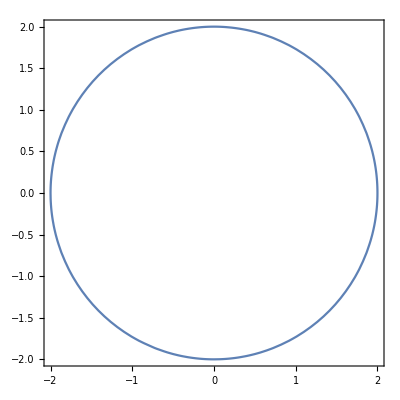

```mathematica
ContourPlot[x^2+y^2==4,{x,-2,2},{y,-2,2}]
```

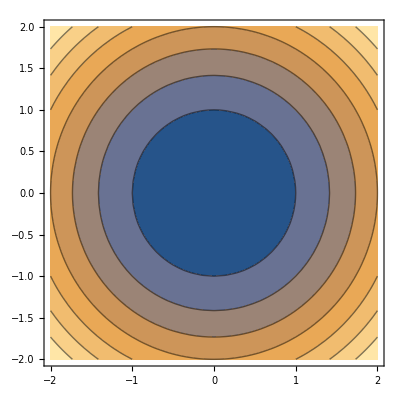

```mathematica
ContourPlot[x^2+y^2,{x,-2,2},{y,-2,2}]
```

```mathematica
Show[
ContourPlot3D[v1.(r-l1[0])==0,{x,-5,5},{y,-5,5},{z,-5,5},ContourStyle-> Blue],
ParametricPlot3D[
l1[t],{t,-2,2},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->15,PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[{x+y+z==0,v1.(r-l1[0])==0},{x,-5,5},{y,-5,5},{z,-5,5},ContourStyle-> {Cyan,Magenta}],
ParametricPlot3D[
l1[t],{t,-2,2},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->15,PlotStyle->Red]
]
```

-Graphics3D-

```mathematica
(*2 solutions, 3 unknowns -> underconstrained*)
```

```mathematica
intline[t_]={t,(-t-(5-3t)/4),(5-3t)/4}
```

{t,-t+1/4 (-5+3 t),1/4 (5-3 t)}

```mathematica
intline[t]//Simplify
```

{t,1/4 (-5-t),1/4 (5-3 t)}

```mathematica
Show[
ContourPlot3D[{x+y+z==0,v1.(r-l1[0])==0},{x,-5,5},{y,-5,5},{z,-5,5},ContourStyle-> {Cyan,Magenta}],
ParametricPlot3D[
intline[t],{t,-5,5},Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->15,PlotStyle->{Thickness[0.05],Red}]
]
```

-Graphics3D-